## Important definitions

```mathematica
{Energy1[δϕ_,λ_,kx_,ky_,kz_],Energy2[δϕ_,λ_,kx_,ky_,kz_],Energy3[δϕ_,λ_,kx_,ky_,kz_]}:={Root[-6 kx ky kz δϕ+2 kx ky kz δϕ^3+(-kx^2-ky^2-kz^2-kx^2 δϕ^2-ky^2 δϕ^2-kz^2 δϕ^2) #1+#1^3&,1],Root[-6 kx ky kz δϕ+2 kx ky kz δϕ^3+(-kx^2-ky^2-kz^2-kx^2 δϕ^2-ky^2 δϕ^2-kz^2 δϕ^2) #1+#1^3&,2]+λ(kx^2+ky^2+kz^2),Root[-6 kx ky kz δϕ+2 kx ky kz δϕ^3+(-kx^2-ky^2-kz^2-kx^2 δϕ^2-ky^2 δϕ^2-kz^2 δϕ^2) #1+#1^3&,3]};
```

## δϕ = 0.1 λ = 0.1

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,4583237},{0.1,4933711},{0.11,5232793},{0.12,5495785},{0.13,5732817},{0.14,5949257},{0.15,6147133},{0.16,6328497},{0.17,6497225},{0.18,6651493},{0.19,6794253},{0.2,6926297}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,4583237},{0.1,4933711},{0.11,5232793},{0.12,5495785},{0.13,5732817},{0.14,5949257},{0.15,6147133},{0.16,6328497},{0.17,6497225},{0.18,6651493},{0.19,6794253},{0.2,6926297}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.00663411},{-0.03,0.048083},{-0.02,0.077058},{-0.01,0.102978},{0.,0.133038},{0.01,0.156322},{0.02,0.175435},{0.03,0.19276},{0.04,0.207882},{0.05,0.20342},{0.06,0.188839},{0.07,0.172604},{0.08,0.155211},{0.09,0.139193},{0.1,0.118783},{0.11,0.104449},{0.12,0.0941389},{0.13,0.0859607},{0.14,0.0785878},{0.15,0.07203},{0.16,0.0670115},{0.17,0.0612686},{0.18,0.0566981},{0.19,0.0524422}}

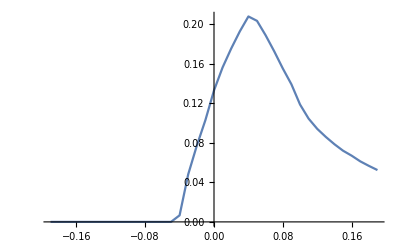

48.6042987

```mathematica
t0=AbsoluteTime[];
Band2 = Table[Energy2[0.1,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2 = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2[[i,1]]=-0.21+0.01 i;If[Band2[[x,y,z]]<-0.21+0.01 i,NDens2[[i,2]]=NDens2[[i,2]]+1]
]
]
]
]
DDens2=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2[[i,1]]=-0.2+0.01 i;DDens2[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2[[i+2,2]]-NDens2[[i+1,2]])]
DDens2
ListLinePlot[DDens2]
t=(AbsoluteTime[]-t0)/60
```

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000309782},{0.03,0.0000627508},{0.04,0.0000945234},{0.05,0.00015648},{0.06,0.000204139},{0.07,0.000275627},{0.08,0.000370945},{0.09,0.000453553},{0.1,0.000532985},{0.11,0.000647366},{0.12,0.000780811},{0.13,0.000899958},{0.14,0.00108265},{0.15,0.00116049},{0.16,0.00134477},{0.17,0.00155288},{0.18,0.00163867},{0.19,0.00195322}}

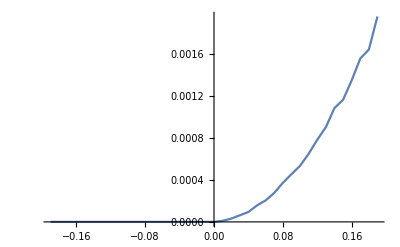

```mathematica
Band3 = Table[Energy3[0.1,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens3 = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens3[[i,1]]=-0.21+0.01 i;If[Band3[[x,y,z]]<-0.21+0.01 i,NDens3[[i,2]]=NDens3[[i,2]]+1]
]
]
]
]

DDens3=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3[[i,1]]=-0.2+0.01 i;
DDens3[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3[[i+2,2]]-NDens3[[i+1,2]])]
DDens3
ListLinePlot[DDens3]
```

Set::partw: Part 42 of {{0,0},{-0.19,8092148},{-0.18,8096274},{-0.17,8100184},{-0.16,8103570},{-0.15,8106492},{-0.14,8109218},{-0.13,8111484},{-0.12,8113450},{-0.11,8115080},{-0.1,8116422},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,8092148},{-0.18,8096274},{-0.17,8100184},{-0.16,8103570},{-0.15,8106492},{-0.14,8109218},{-0.13,8111484},{-0.12,8113450},{-0.11,8115080},{-0.1,8116422},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,8092148},{-0.18,8096274},{-0.17,8100184},{-0.16,8103570},{-0.15,8106492},{-0.14,8109218},{-0.13,8111484},{-0.12,8113450},{-0.11,8115080},{-0.1,8116422},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,8092148},{-0.18,8096274},{-0.17,8100184},{-0.16,8103570},{-0.15,8106492},{-0.14,8109218},{-0.13,8111484},{-0.12,8113450},{-0.11,8115080},{-0.1,8116422},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.00163867},{-0.18,0.00155288},{-0.17,0.00134477},{-0.16,0.00116049},{-0.15,0.00108265},{-0.14,0.000899958},{-0.13,0.000780811},{-0.12,0.000647366},{-0.11,0.000532985},{-0.1,0.000453553},{-0.09,0.000370945},{-0.08,0.000275627},{-0.07,0.000204139},{-0.06,0.00015648},{-0.05,0.0000945234},{-0.04,0.0000627508},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

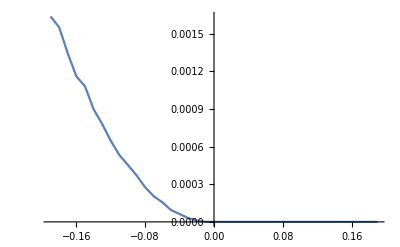

```mathematica
Band1 = Table[Energy1[0.1,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens1 = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens1[[i,1]]=-0.21+0.01 i;If[Band1[[x,y,z]]<-0.21+0.01 i,NDens1[[i,2]]=NDens1[[i,2]]+1]
]
]
]
]

DDens1=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1[[i,1]]=-0.2+0.01 i;DDens1[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1[[i+2,2]]-NDens1[[i+1,2]]]]
DDens1
ListLinePlot[DDens1]
```

{{-0.19,0.00163867},{-0.18,0.00155288},{-0.17,0.00134477},{-0.16,0.00116049},{-0.15,0.00108265},{-0.14,0.000899958},{-0.13,0.000780811},{-0.12,0.000647366},{-0.11,0.000532985},{-0.1,0.000453553},{-0.09,0.000370945},{-0.08,0.000275627},{-0.07,0.000204139},{-0.06,0.00015648},{-0.05,0.0000945234},{-0.04,0.00669686},{-0.03,0.048114},{-0.02,0.0770683},{-0.01,0.102978},{0.,0.133038},{0.01,0.156332},{0.02,0.175466},{0.03,0.192823},{0.04,0.207977},{0.05,0.203576},{0.06,0.189043},{0.07,0.17288},{0.08,0.155582},{0.09,0.139647},{0.1,0.119315},{0.11,0.105096},{0.12,0.0949197},{0.13,0.0868606},{0.14,0.0796705},{0.15,0.0731905},{0.16,0.0683563},{0.17,0.0628215},{0.18,0.0583368},{0.19,0.0543954}}

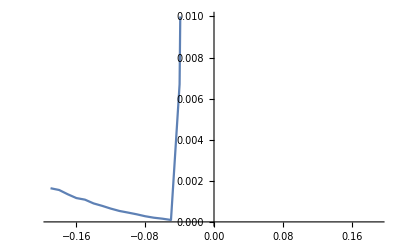

```mathematica
DDensT=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensT[[i,1]]=DDens1[[i,1]];DDensT[[i,2]]=DDens1[[i,2]]+DDens2[[i,2]]+DDens3[[i,2]]]
DDensT
ListLinePlot[DDensT,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0.05 λ = 0.1 (b)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,3966801},{0.1,4589487},{0.11,5119725},{0.12,5569277},{0.13,5959165},{0.14,6294125},{0.15,6579997},{0.16,6817737},{0.17,7014817},{0.18,7181489},{0.19,7324629},{0.2,7449589}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,3966801},{0.1,4589487},{0.11,5119725},{0.12,5569277},{0.13,5959165},{0.14,6294125},{0.15,6579997},{0.16,6817737},{0.17,7014817},{0.18,7181489},{0.19,7324629},{0.2,7449589}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.0297153},{0.,0.0822874},{0.01,0.114841},{0.02,0.13957},{0.03,0.160425},{0.04,0.178493},{0.05,0.195821},{0.06,0.210666},{0.07,0.224711},{0.08,0.238911},{0.09,0.247304},{0.1,0.210588},{0.11,0.178543},{0.12,0.154847},{0.13,0.133032},{0.14,0.113536},{0.15,0.0944201},{0.16,0.0782717},{0.17,0.0661949},{0.18,0.0568491},{0.19,0.0496287}}

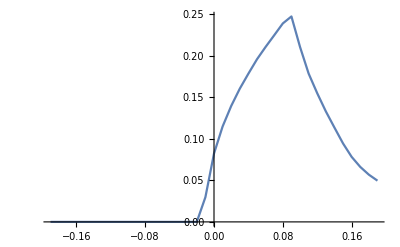

48.7984074

```mathematica
t0=AbsoluteTime[];
Band2b = Table[Energy2[0.05,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2b = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2b[[i,1]]=-0.21+0.01 i;If[Band2b[[x,y,z]]<-0.21+0.01 i,NDens2b[[i,2]]=NDens2b[[i,2]]+1]
]
]
]
]
DDens2b=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2b[[i,1]]=-0.2+0.01 i;DDens2b[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2b[[i+2,2]]-NDens2b[[i+1,2]])]
DDens2b
ListLinePlot[DDens2b]
t=(AbsoluteTime[]-t0)/60
```

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«15»,{0.08,2139},{0.09,3029},{0.1,4139},{0.11,5569},{0.12,7139},{0.13,9129},{0.14,11395},{0.15,14117},{0.16,17091},{0.17,20429},{0.18,24339},{0.19,28585},{0.2,33443}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«15»,{0.08,2139},{0.09,3029},{0.1,4139},{0.11,5569},{0.12,7139},{0.13,9129},{0.14,11395},{0.15,14117},{0.16,17091},{0.17,20429},{0.18,24339},{0.19,28585},{0.2,33443}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000309782},{0.03,0.0000579849},{0.04,0.0000881689},{0.05,0.000172366},{0.06,0.000199373},{0.07,0.000289925},{0.08,0.00035347},{0.09,0.000440844},{0.1,0.000567934},{0.11,0.000623536},{0.12,0.000790342},{0.13,0.000899958},{0.14,0.00108106},{0.15,0.00118114},{0.16,0.00132571},{0.17,0.00155288},{0.18,0.00168633},{0.19,0.00192939}}

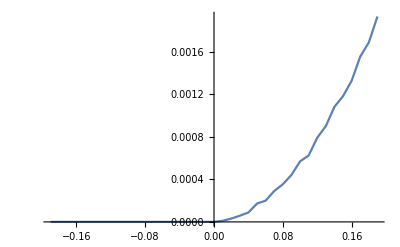

```mathematica
Band3b = Table[Energy3[0.05,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens3b = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens3b[[i,1]]=-0.21+0.01 i;If[Band3b[[x,y,z]]<-0.21+0.01 i,NDens3b[[i,2]]=NDens3b[[i,2]]+1]
]
]
]
]

DDens3b=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3b[[i,1]]=-0.2+0.01 i;
DDens3b[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3b[[i+2,2]]-NDens3b[[i+1,2]])]
DDens3b
ListLinePlot[DDens3b]
```

Set::partw: Part 42 of {{0,0},{-0.19,8092016},{-0.18,8096262},{-0.17,8100172},{-0.16,8103510},{-0.15,8106484},{-0.14,8109206},{-0.13,8111472},{-0.12,8113462},{-0.11,8115032},{-0.1,8116462},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,8092016},{-0.18,8096262},{-0.17,8100172},{-0.16,8103510},{-0.15,8106484},{-0.14,8109206},{-0.13,8111472},{-0.12,8113462},{-0.11,8115032},{-0.1,8116462},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,8092016},{-0.18,8096262},{-0.17,8100172},{-0.16,8103510},{-0.15,8106484},{-0.14,8109206},{-0.13,8111472},{-0.12,8113462},{-0.11,8115032},{-0.1,8116462},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,8092016},{-0.18,8096262},{-0.17,8100172},{-0.16,8103510},{-0.15,8106484},{-0.14,8109206},{-0.13,8111472},{-0.12,8113462},{-0.11,8115032},{-0.1,8116462},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

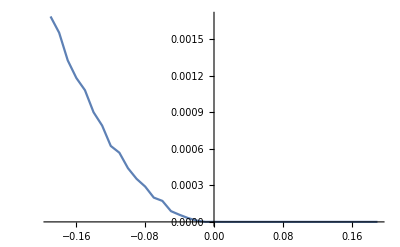

```mathematica
Band1b = Table[Energy1[0.05,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens1b = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens1b[[i,1]]=-0.21+0.01 i;If[Band1b[[x,y,z]]<-0.21+0.01 i,NDens1b[[i,2]]=NDens1b[[i,2]]+1]
]
]
]
]

DDens1b=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1b[[i,1]]=-0.2+0.01 i;DDens1b[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1b[[i+2,2]]-NDens1b[[i+1,2]]]]
DDens1b
ListLinePlot[DDens1b]
```

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.0297153},{0.,0.0822881},{0.01,0.114851},{0.02,0.139601},{0.03,0.160483},{0.04,0.178581},{0.05,0.195994},{0.06,0.210866},{0.07,0.225001},{0.08,0.239265},{0.09,0.247745},{0.1,0.211156},{0.11,0.179166},{0.12,0.155637},{0.13,0.133932},{0.14,0.114617},{0.15,0.0956012},{0.16,0.0795974},{0.17,0.0677478},{0.18,0.0585354},{0.19,0.0515581}}

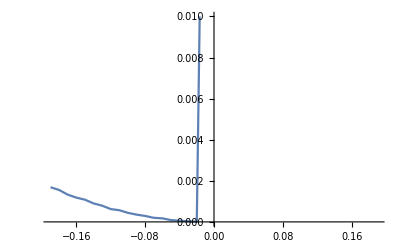

```mathematica
DDensTb=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTb[[i,1]]=DDens1b[[i,1]];DDensTb[[i,2]]=DDens1b[[i,2]]+DDens2b[[i,2]]+DDens3b[[i,2]]]
DDensTb
ListLinePlot[DDensTb,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0 λ = 0.1 (c)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,3575377},{0.1,4187707},{0.11,4795537},{0.12,5341309},{0.13,5831225},{0.14,6265733},{0.15,6646929},{0.16,6976821},{0.17,7257097},{0.18,7489577},{0.19,7674717},{0.2,7814341}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,3575377},{0.1,4187707},{0.11,4795537},{0.12,5341309},{0.13,5831225},{0.14,6265733},{0.15,6646929},{0.16,6976821},{0.17,7257097},{0.18,7489577},{0.19,7674717},{0.2,7814341}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,0.0525466},{0.01,0.0962145},{0.02,0.124466},{0.03,0.147522},{0.04,0.167212},{0.05,0.185103},{0.06,0.201085},{0.07,0.216071},{0.08,0.229766},{0.09,0.243191},{0.1,0.241404},{0.11,0.216757},{0.12,0.194574},{0.13,0.172568},{0.14,0.151395},{0.15,0.131019},{0.16,0.111314},{0.17,0.0923311},{0.18,0.0735296},{0.19,0.0554526}}

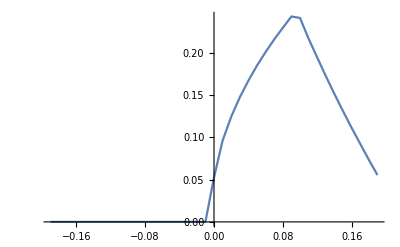

48.6721144

```mathematica
t0=AbsoluteTime[];
Band2c = Table[Energy2[0,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2c = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2c[[i,1]]=-0.21+0.01 i;If[Band2c[[x,y,z]]<-0.21+0.01 i,NDens2c[[i,2]]=NDens2c[[i,2]]+1]
]
]
]
]
DDens2c=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2c[[i,1]]=-0.2+0.01 i;DDens2c[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2c[[i+2,2]]-NDens2c[[i+1,2]])]
DDens2c
ListLinePlot[DDens2c]
t=(AbsoluteTime[]-t0)/60
```

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«15»,{0.08,2103},{0.09,2969},{0.1,4139},{0.11,5497},{0.12,7123},{0.13,9093},{0.14,11459},{0.15,13997},{0.16,17071},{0.17,20377},{0.18,24303},{0.19,28545},{0.2,33371}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«15»,{0.08,2103},{0.09,2969},{0.1,4139},{0.11,5497},{0.12,7123},{0.13,9093},{0.14,11459},{0.15,13997},{0.16,17071},{0.17,20377},{0.18,24303},{0.19,28545},{0.2,33371}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000262124},{0.03,0.0000627508},{0.04,0.0000929347},{0.05,0.000162834},{0.06,0.000186664},{0.07,0.000293102},{0.08,0.000343938},{0.09,0.000464674},{0.1,0.000539339},{0.11,0.000645777},{0.12,0.000782399},{0.13,0.000939673},{0.14,0.00100798},{0.15,0.00122086},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

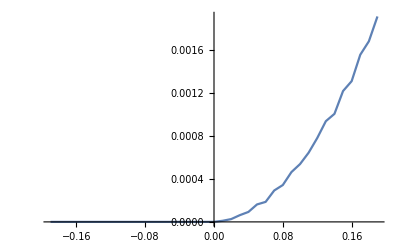

```mathematica
Band3c = Table[Energy3[0,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens3c = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens3c[[i,1]]=-0.21+0.01 i;If[Band3c[[x,y,z]]<-0.21+0.01 i,NDens3c[[i,2]]=NDens3c[[i,2]]+1]
]
]
]
]

DDens3c=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3c[[i,1]]=-0.2+0.01 i;
DDens3c[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3c[[i+2,2]]-NDens3c[[i+1,2]])]
DDens3c
ListLinePlot[DDens3c]
```

Set::partw: Part 42 of {{0,0},{-0.19,8091930},{-0.18,8096196},{-0.17,8100122},{-0.16,8103524},{-0.15,8106454},{-0.14,8109088},{-0.13,8111430},{-0.12,8113448},{-0.11,8115026},{-0.1,8116432},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,8091930},{-0.18,8096196},{-0.17,8100122},{-0.16,8103524},{-0.15,8106454},{-0.14,8109088},{-0.13,8111430},{-0.12,8113448},{-0.11,8115026},{-0.1,8116432},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,8091930},{-0.18,8096196},{-0.17,8100122},{-0.16,8103524},{-0.15,8106454},{-0.14,8109088},{-0.13,8111430},{-0.12,8113448},{-0.11,8115026},{-0.1,8116432},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,8091930},{-0.18,8096196},{-0.17,8100122},{-0.16,8103524},{-0.15,8106454},{-0.14,8109088},{-0.13,8111430},{-0.12,8113448},{-0.11,8115026},{-0.1,8116432},«19»,{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

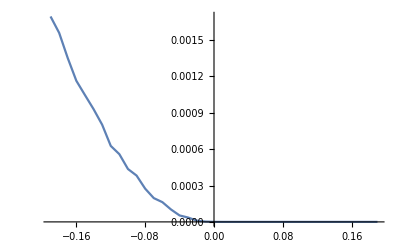

```mathematica
Band1c = Table[Energy1[0,0.1,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens1c = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens1c[[i,1]]=-0.21+0.01 i;If[Band1c[[x,y,z]]<-0.21+0.01 i,NDens1c[[i,2]]=NDens1c[[i,2]]+1]
]
]
]
]

DDens1c=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1c[[i,1]]=-0.2+0.01 i;DDens1c[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1c[[i+2,2]]-NDens1c[[i+1,2]]]]
DDens1c
ListLinePlot[DDens1c]
```

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,0.0525474},{0.01,0.0962248},{0.02,0.124492},{0.03,0.147585},{0.04,0.167305},{0.05,0.185266},{0.06,0.201272},{0.07,0.216364},{0.08,0.23011},{0.09,0.243656},{0.1,0.241943},{0.11,0.217403},{0.12,0.195356},{0.13,0.173508},{0.14,0.152403},{0.15,0.13224},{0.16,0.112627},{0.17,0.0938903},{0.18,0.0752144},{0.19,0.0573693}}

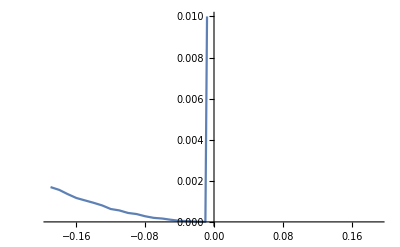

```mathematica
DDensTc=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTc[[i,1]]=DDens1c[[i,1]];DDensTc[[i,2]]=DDens1c[[i,2]]+DDens2c[[i,2]]+DDens3c[[i,2]]]
DDensTc
ListLinePlot[DDensTc,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0 λ = 0.05 (d)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,7489577},{0.1,7814341},{0.11,7981905},{0.12,8066609},{0.13,8104993},{0.14,8118313},{0.15,8120593},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,7489577},{0.1,7814341},{0.11,7981905},{0.12,8066609},{0.13,8104993},{0.14,8118313},{0.15,8120593},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,7489577},{0.1,7814341},{0.11,7981905},{0.12,8066609},{0.13,8104993},{0.14,8118313},{0.15,8120593},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,7489577},{0.1,7814341},{0.11,7981905},{0.12,8066609},{0.13,8104993},{0.14,8118313},{0.15,8120593},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,0.148761},{0.01,0.271988},{0.02,0.352315},{0.03,0.417156},{0.04,0.472957},{0.05,0.458161},{0.06,0.367141},{0.07,0.282414},{0.08,0.203645},{0.09,0.128982},{0.1,0.0665492},{0.11,0.0336408},{0.12,0.0152445},{0.13,0.00529013},{0.14,0.000905518},{0.15,3.17726×10^-6},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

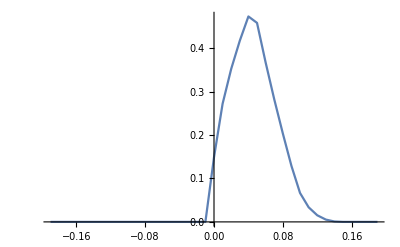

51.7827326

```mathematica
t0=AbsoluteTime[];
Band2d = Table[Energy2[0,0.05,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2d = Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2d[[i,1]]=-0.21+0.01 i;If[Band2d[[x,y,z]]<-0.21+0.01 i,NDens2d[[i,2]]=NDens2d[[i,2]]+1]
]
]
]
]
DDens2d=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2d[[i,1]]=-0.2+0.01 i;DDens2d[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2d[[i+2,2]]-NDens2d[[i+1,2]])]
DDens2d
ListLinePlot[DDens2d]
t=(AbsoluteTime[]-t0)/60
```

```mathematica
(*band 1,3 和 λ 无关, 直接调用前三次的计算结果, 选取相同的 δϕ 值就可以*)
NDens3d = Table[0,{i,1,41},{j,1,2}];
NDens3d=NDens3c;
DDens3d=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3d[[i,1]]=-0.2+0.01 i;
DDens3d[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3d[[i+2,2]]-NDens3d[[i+1,2]])]
DDens3d
ListLinePlot[DDens3d]
```

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000262124},{0.03,0.0000627508},{0.04,0.0000929347},{0.05,0.000162834},{0.06,0.000186664},{0.07,0.000293102},{0.08,0.000343938},{0.09,0.000464674},{0.1,0.000539339},{0.11,0.000645777},{0.12,0.000782399},{0.13,0.000939673},{0.14,0.00100798},{0.15,0.00122086},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

-Graphics-

```mathematica
NDens1d = Table[0,{i,1,41},{j,1,2}];
NDens1d=NDens1c;
DDens1d=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1d[[i,1]]=-0.2+0.01 i;
DDens1d[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens1d[[i+2,2]]-NDens1d[[i+1,2]])]
DDens1d
ListLinePlot[DDens1d]
```

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

-Graphics-

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,0.148762},{0.01,0.271999},{0.02,0.352341},{0.03,0.417219},{0.04,0.47305},{0.05,0.458324},{0.06,0.367328},{0.07,0.282707},{0.08,0.203989},{0.09,0.129447},{0.1,0.0670886},{0.11,0.0342866},{0.12,0.0160269},{0.13,0.0062298},{0.14,0.0019135},{0.15,0.00122404},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

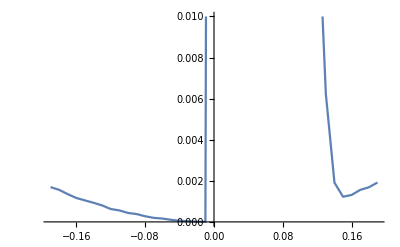

```mathematica
DDensTd=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTd[[i,1]]=DDens1d[[i,1]];DDensTd[[i,2]]=DDens1d[[i,2]]+DDens2d[[i,2]]+DDens3d[[i,2]]]
DDensTd
ListLinePlot[DDensTd,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0 λ = 0 (e)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,8120601},{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,8120601},{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,8120601},{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,8120601},{0.1,8120601},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.22515},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

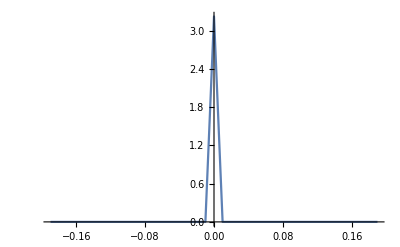

52.3160936

```mathematica
t0=AbsoluteTime[];
Band2e= Table[Energy2[0,0,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2e= Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2e[[i,1]]=-0.21+0.01 i;If[Band2e[[x,y,z]]<-0.21+0.01 i,NDens2e[[i,2]]=NDens2e[[i,2]]+1]
]
]
]
]
DDens2e=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2e[[i,1]]=-0.2+0.01 i;DDens2e[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2e[[i+2,2]]-NDens2e[[i+1,2]])]
DDens2e
ListLinePlot[DDens2e]
t=(AbsoluteTime[]-t0)/60
```

```mathematica
NDens3e = Table[0,{i,1,41},{j,1,2}];
NDens3e=NDens3c;

DDens3e=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3e[[i,1]]=-0.2+0.01 i;
DDens3e[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3e[[i+2,2]]-NDens3e[[i+1,2]])]
DDens3e
ListLinePlot[DDens3e]
```

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000262124},{0.03,0.0000627508},{0.04,0.0000929347},{0.05,0.000162834},{0.06,0.000186664},{0.07,0.000293102},{0.08,0.000343938},{0.09,0.000464674},{0.1,0.000539339},{0.11,0.000645777},{0.12,0.000782399},{0.13,0.000939673},{0.14,0.00100798},{0.15,0.00122086},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

-Graphics-

```mathematica
NDens1e = Table[0,{i,1,41},{j,1,2}];
NDens1e=NDens1c;

DDens1e=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1e[[i,1]]=-0.2+0.01 i;DDens1e[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1e[[i+2,2]]-NDens1e[[i+1,2]]]]
DDens1e
ListLinePlot[DDens1e]
```

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

-Graphics-

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,3.22515},{0.01,0.0000103261},{0.02,0.0000262124},{0.03,0.0000627508},{0.04,0.0000929347},{0.05,0.000162834},{0.06,0.000186664},{0.07,0.000293102},{0.08,0.000343938},{0.09,0.000464674},{0.1,0.000539339},{0.11,0.000645777},{0.12,0.000782399},{0.13,0.000939673},{0.14,0.00100798},{0.15,0.00122086},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

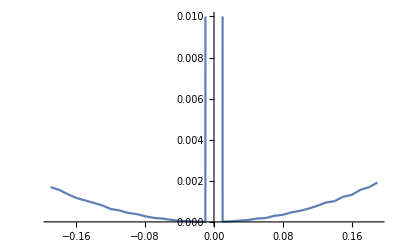

```mathematica
DDensTe=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTe[[i,1]]=DDens1e[[i,1]];DDensTe[[i,2]]=DDens1e[[i,2]]+DDens2e[[i,2]]+DDens3e[[i,2]]]
DDensTe
ListLinePlot[DDensTe,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0.05 λ = 0 (f)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,15184},«17»,{0.09,8105413},{0.1,8120597},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,15184},«17»,{0.09,8105413},{0.1,8120597},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,15184},«17»,{0.09,8105413},{0.1,8120597},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,15184},«17»,{0.09,8105413},{0.1,8120597},{0.11,8120601},{0.12,8120601},{0.13,8120601},{0.14,8120601},{0.15,8120601},{0.16,8120601},{0.17,8120601},{0.18,8120601},{0.19,8120601},{0.2,8120601}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.00603043},{-0.09,0.0298408},{-0.08,0.062225},{-0.07,0.097197},{-0.06,0.132388},{-0.05,0.166626},{-0.04,0.201508},{-0.03,0.238119},{-0.02,0.285092},{-0.01,0.369601},{0.,0.417497},{0.01,0.285092},{0.02,0.238119},{0.03,0.201508},{0.04,0.166626},{0.05,0.132388},{0.06,0.097197},{0.07,0.062225},{0.08,0.0298408},{0.09,0.00603043},{0.1,1.58863×10^-6},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

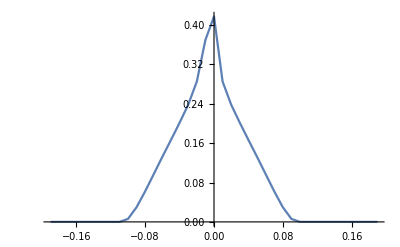

53.2427177

```mathematica
t0=AbsoluteTime[];
Band2f= Table[Energy2[0.05,0,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2f= Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2f[[i,1]]=-0.21+0.01 i;If[Band2f[[x,y,z]]<-0.21+0.01 i,NDens2f[[i,2]]=NDens2f[[i,2]]+1]
]
]
]
]
DDens2f=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2f[[i,1]]=-0.2+0.01 i;DDens2f[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2f[[i+2,2]]-NDens2f[[i+1,2]])]
DDens2f
ListLinePlot[DDens2f]
t=(AbsoluteTime[]-t0)/60
```

```mathematica
NDens3f = Table[0,{i,1,41},{j,1,2}];
NDens3f=NDens3b;

DDens3f=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3f[[i,1]]=-0.2+0.01 i;
DDens3f[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3f[[i+2,2]]-NDens3f[[i+1,2]])]
DDens3f
ListLinePlot[DDens3f]
```

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000309782},{0.03,0.0000579849},{0.04,0.0000881689},{0.05,0.000172366},{0.06,0.000199373},{0.07,0.000289925},{0.08,0.00035347},{0.09,0.000440844},{0.1,0.000567934},{0.11,0.000623536},{0.12,0.000790342},{0.13,0.000899958},{0.14,0.00108106},{0.15,0.00118114},{0.16,0.00132571},{0.17,0.00155288},{0.18,0.00168633},{0.19,0.00192939}}

-Graphics-

```mathematica
NDens1f = Table[0,{i,1,41},{j,1,2}];
NDens1f=NDens1b;

DDens1f=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1f[[i,1]]=-0.2+0.01 i;DDens1f[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1f[[i+2,2]]-NDens1f[[i+1,2]]]]
DDens1f
ListLinePlot[DDens1f]
```

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

-Graphics-

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.00647128},{-0.09,0.0301943},{-0.08,0.0625149},{-0.07,0.0973964},{-0.06,0.132561},{-0.05,0.166715},{-0.04,0.201566},{-0.03,0.23815},{-0.02,0.285102},{-0.01,0.369601},{0.,0.417497},{0.01,0.285102},{0.02,0.23815},{0.03,0.201566},{0.04,0.166715},{0.05,0.132561},{0.06,0.0973964},{0.07,0.0625149},{0.08,0.0301943},{0.09,0.00647128},{0.1,0.000569523},{0.11,0.000623536},{0.12,0.000790342},{0.13,0.000899958},{0.14,0.00108106},{0.15,0.00118114},{0.16,0.00132571},{0.17,0.00155288},{0.18,0.00168633},{0.19,0.00192939}}

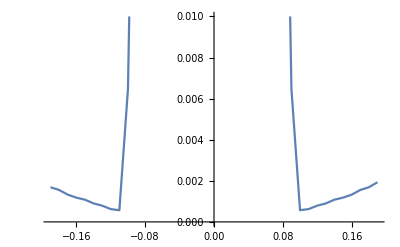

```mathematica
DDensTf=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTf[[i,1]]=DDens1f[[i,1]];DDensTf[[i,2]]=DDens1f[[i,2]]+DDens2f[[i,2]]+DDens3f[[i,2]]]
DDensTf
ListLinePlot[DDensTf,PlotRange->{0,0.01},ClippingStyle->None]
```

## δϕ = 0.05 λ = 0.05 (g)

Set::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,6645721},{0.1,6921197},{0.11,7156101},{0.12,7355389},{0.13,7523605},{0.14,7663801},{0.15,7779521},{0.16,7873193},{0.17,7947281},{0.18,8004821},{0.19,8047553},{0.2,8078029}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Part::partw: Part 42 of {{0,0},{-0.19,0},{-0.18,0},{-0.17,0},{-0.16,0},{-0.15,0},{-0.14,0},{-0.13,0},{-0.12,0},{-0.11,0},{-0.1,0},{-0.09,0},{-0.08,0},«16»,{0.09,6645721},{0.1,6921197},{0.11,7156101},{0.12,7355389},{0.13,7523605},{0.14,7663801},{0.15,7779521},{0.16,7873193},{0.17,7947281},{0.18,8004821},{0.19,8047553},{0.2,8078029}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.0557894},{-0.01,0.181633},{0.,0.290046},{0.01,0.369153},{0.02,0.410835},{0.03,0.358927},{0.04,0.292736},{0.05,0.22246},{0.06,0.179308},{0.07,0.150394},{0.08,0.128113},{0.09,0.109407},{0.1,0.0932938},{0.11,0.0791486},{0.12,0.0668082},{0.13,0.0556798},{0.14,0.045959},{0.15,0.0372025},{0.16,0.0294246},{0.17,0.0228524},{0.18,0.0169713},{0.19,0.0121038}}

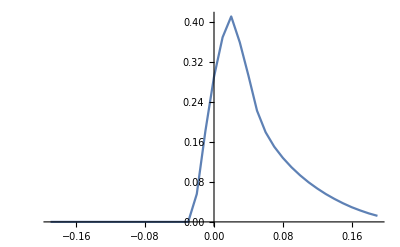

50.90559

```mathematica
t0=AbsoluteTime[];
Band2g= Table[Energy2[0.05,0.05,kx,ky,kz],{kx,-1,1,0.01},{ky,-1,1,0.01},{kz,-1,1,0.01}];
NDens2g= Table[0,{i,1,41},{j,1,2}];
For[i=1,i≤41,i=i+1;
For[x=1,x≤201,x=x+1,
For[
y=1,y≤201,y=y+1,
For[z=1,z≤201,z=z+1,NDens2g[[i,1]]=-0.21+0.01 i;If[Band2g[[x,y,z]]<-0.21+0.01 i,NDens2g[[i,2]]=NDens2g[[i,2]]+1]
]
]
]
]
DDens2g=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens2g[[i,1]]=-0.2+0.01 i;DDens2g[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens2g[[i+2,2]]-NDens2g[[i+1,2]])]
DDens2g
ListLinePlot[DDens2g]
t=(AbsoluteTime[]-t0)/60
```

```mathematica
NDens3g = Table[0,{i,1,41},{j,1,2}];
NDens3g=NDens3b;

DDens3g=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens3g[[i,1]]=-0.2+0.01 i;
DDens3g[[i,2]]=1/(2π)^3*1/0.01*8/201^3(NDens3g[[i+2,2]]-NDens3g[[i+1,2]])]
DDens3g
ListLinePlot[DDens3g]
```

{{-0.19,0.},{-0.18,0.},{-0.17,0.},{-0.16,0.},{-0.15,0.},{-0.14,0.},{-0.13,0.},{-0.12,0.},{-0.11,0.},{-0.1,0.},{-0.09,0.},{-0.08,0.},{-0.07,0.},{-0.06,0.},{-0.05,0.},{-0.04,0.},{-0.03,0.},{-0.02,0.},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.0000103261},{0.02,0.0000309782},{0.03,0.0000579849},{0.04,0.0000881689},{0.05,0.000172366},{0.06,0.000199373},{0.07,0.000289925},{0.08,0.00035347},{0.09,0.000440844},{0.1,0.000567934},{0.11,0.000623536},{0.12,0.000790342},{0.13,0.000899958},{0.14,0.00108106},{0.15,0.00118114},{0.16,0.00132571},{0.17,0.00155288},{0.18,0.00168633},{0.19,0.00192939}}

-Graphics-

```mathematica
NDens1g = Table[0,{i,1,41},{j,1,2}];
NDens1g=NDens1b;

DDens1g=Table[0,{i,1,39},{j,2}];
For[i=1,i≤39,i++,DDens1g[[i,1]]=-0.2+0.01 i;DDens1g[[i,2]]=1/(2π)^3*1/0.01*8/201^3 Abs[NDens1g[[i+2,2]]-NDens1g[[i+1,2]]]]
DDens1g
ListLinePlot[DDens1g]
```

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.},{0.,3.97157×10^-7},{0.01,0.},{0.02,0.},{0.03,0.},{0.04,0.},{0.05,0.},{0.06,0.},{0.07,0.},{0.08,0.},{0.09,0.},{0.1,0.},{0.11,0.},{0.12,0.},{0.13,0.},{0.14,0.},{0.15,0.},{0.16,0.},{0.17,0.},{0.18,0.},{0.19,0.}}

-Graphics-

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0557998},{-0.01,0.181633},{0.,0.290047},{0.01,0.369164},{0.02,0.410866},{0.03,0.358985},{0.04,0.292825},{0.05,0.222632},{0.06,0.179508},{0.07,0.150684},{0.08,0.128467},{0.09,0.109848},{0.1,0.0938617},{0.11,0.0797722},{0.12,0.0675985},{0.13,0.0565798},{0.14,0.0470401},{0.15,0.0383836},{0.16,0.0307503},{0.17,0.0244053},{0.18,0.0186576},{0.19,0.0140331}}

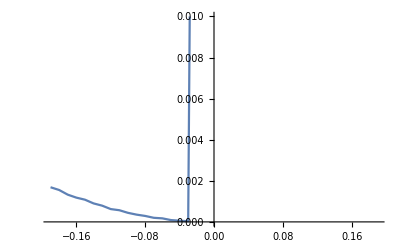

```mathematica
DDensTg=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,DDensTg[[i,1]]=DDens1g[[i,1]];DDensTg[[i,2]]=DDens1g[[i,2]]+DDens2g[[i,2]]+DDens3g[[i,2]]]
DDensTg
ListLinePlot[DDensTg,PlotRange->{0,0.01},ClippingStyle->None]
```

## Figures

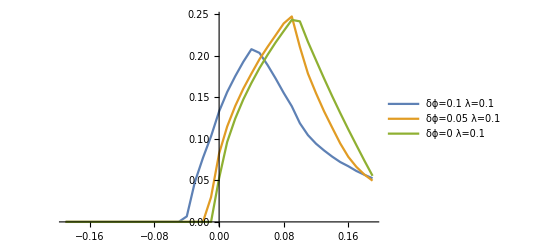

```mathematica
ListLinePlot[{DDens2,DDens2b,DDens2c},PlotLegends->{"δϕ=0.1 λ=0.1","δϕ=0.05 λ=0.1","δϕ=0 λ=0.1"}](*flat band density of state*)(**)
```

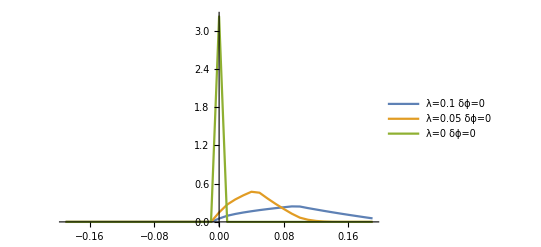

```mathematica
ListLinePlot[{DDens2c,DDens2d,DDens2e},PlotRange->All,PlotLegends->{"λ=0.1 δϕ=0","λ=0.05 δϕ=0","λ=0 δϕ=0"}]
```

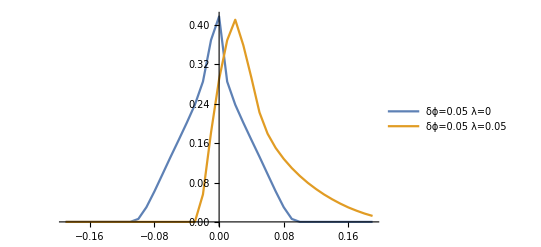

```mathematica
ListLinePlot[{DDens2f,DDens2g},PlotLegends->{"δϕ=0.05 λ=0","δϕ=0.05 λ=0.05"}]
```

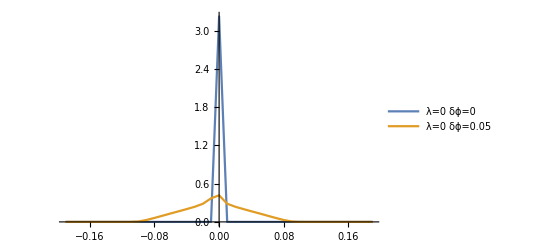

```mathematica
ListLinePlot[{DDens2e,DDens2f},PlotRange->All,PlotLegends->{"λ=0 δϕ=0","λ=0 δϕ=0.05"}]
```

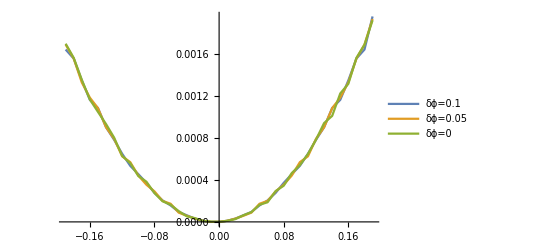

```mathematica
(*band 1 and 3 density of state*)
Dens13=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,Dens13[[i,1]]=DDens1[[i,1]];Dens13[[i,2]]=DDens1[[i,2]]+DDens3[[i,2]]];
Dens13b=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,Dens13b[[i,1]]=DDens1b[[i,1]];Dens13b[[i,2]]=DDens1b[[i,2]]+DDens3b[[i,2]]];
Dens13c=Table[0,{i,39},{j,2}];
For[i=1,i≤39,i++,Dens13c[[i,1]]=DDens1c[[i,1]];Dens13c[[i,2]]=DDens1c[[i,2]]+DDens3c[[i,2]]];
ListLinePlot[{Dens13,Dens13b,Dens13c},PlotRange->All,PlotLegends->{"δϕ=0.1","δϕ=0.05","δϕ=0"}]
```

## Log Figures

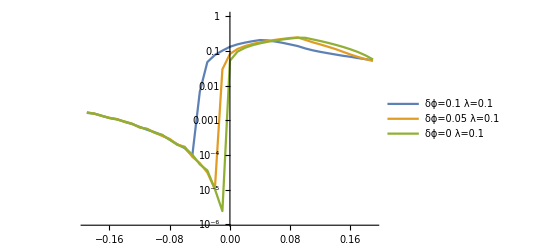

```mathematica
ListLogPlot[{DDensT,DDensTb,DDensTc},Joined->True,PlotLegends->{"δϕ=0.1 λ=0.1","δϕ=0.05 λ=0.1","δϕ=0 λ=0.1"}]
```

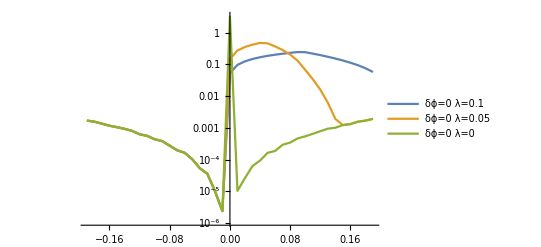

```mathematica
ListLogPlot[{DDensTc,DDensTd,DDensTe},Joined->True,PlotLegends->{"δϕ=0 λ=0.1","δϕ=0 λ=0.05","δϕ=0 λ=0"}]
```

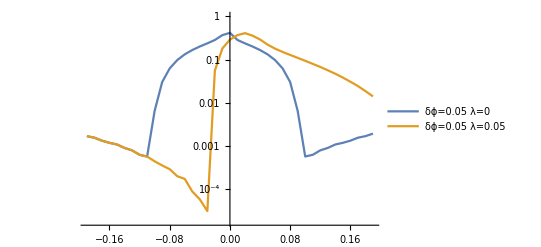

```mathematica
ListLogPlot[{DDensTf,DDensTg},Joined->True,PlotLegends->{"δϕ=0.05 λ=0","δϕ=0.05 λ=0.05"}]
```

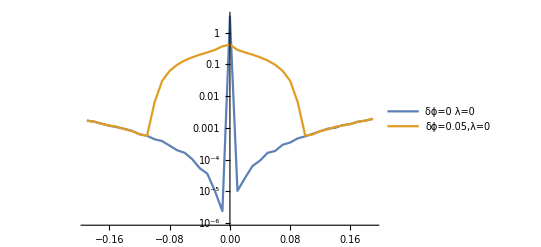

```mathematica
ListLogPlot[{DDensTe,DDensTf},Joined->True,PlotLegends->{"δϕ=0 λ=0","δϕ=0.05,λ=0"}]
```

## Calculation Results

```mathematica
DDensT
DDensTb
DDensTc
DDensTd
DDensTe
DDensTf
DDensTg
```

{{-0.19,0.00163867},{-0.18,0.00155288},{-0.17,0.00134477},{-0.16,0.00116049},{-0.15,0.00108265},{-0.14,0.000899958},{-0.13,0.000780811},{-0.12,0.000647366},{-0.11,0.000532985},{-0.1,0.000453553},{-0.09,0.000370945},{-0.08,0.000275627},{-0.07,0.000204139},{-0.06,0.00015648},{-0.05,0.0000945234},{-0.04,0.00669686},{-0.03,0.048114},{-0.02,0.0770683},{-0.01,0.102978},{0.,0.133038},{0.01,0.156332},{0.02,0.175466},{0.03,0.192823},{0.04,0.207977},{0.05,0.203576},{0.06,0.189043},{0.07,0.17288},{0.08,0.155582},{0.09,0.139647},{0.1,0.119315},{0.11,0.105096},{0.12,0.0949197},{0.13,0.0868606},{0.14,0.0796705},{0.15,0.0731905},{0.16,0.0683563},{0.17,0.0628215},{0.18,0.0583368},{0.19,0.0543954}}

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0000103261},{-0.01,0.0297153},{0.,0.0822881},{0.01,0.114851},{0.02,0.139601},{0.03,0.160483},{0.04,0.178581},{0.05,0.195994},{0.06,0.210866},{0.07,0.225001},{0.08,0.239265},{0.09,0.247745},{0.1,0.211156},{0.11,0.179166},{0.12,0.155637},{0.13,0.133932},{0.14,0.114617},{0.15,0.0956012},{0.16,0.0795974},{0.17,0.0677478},{0.18,0.0585354},{0.19,0.0515581}}

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,0.0525474},{0.01,0.0962248},{0.02,0.124492},{0.03,0.147585},{0.04,0.167305},{0.05,0.185266},{0.06,0.201272},{0.07,0.216364},{0.08,0.23011},{0.09,0.243656},{0.1,0.241943},{0.11,0.217403},{0.12,0.195356},{0.13,0.173508},{0.14,0.152403},{0.15,0.13224},{0.16,0.112627},{0.17,0.0938903},{0.18,0.0752144},{0.19,0.0573693}}

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,0.148762},{0.01,0.271999},{0.02,0.352341},{0.03,0.417219},{0.04,0.47305},{0.05,0.458324},{0.06,0.367328},{0.07,0.282707},{0.08,0.203989},{0.09,0.129447},{0.1,0.0670886},{0.11,0.0342866},{0.12,0.0160269},{0.13,0.0062298},{0.14,0.0019135},{0.15,0.00122404},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

{{-0.19,0.00169427},{-0.18,0.00155924},{-0.17,0.00135113},{-0.16,0.00116367},{-0.15,0.00104611},{-0.14,0.000930142},{-0.13,0.000801463},{-0.12,0.000626714},{-0.11,0.000558403},{-0.1,0.000436078},{-0.09,0.000382065},{-0.08,0.000274038},{-0.07,0.000196196},{-0.06,0.000162834},{-0.05,0.000102467},{-0.04,0.000053219},{-0.03,0.0000357441},{-0.02,0.0000103261},{-0.01,2.38294×10^-6},{0.,3.22515},{0.01,0.0000103261},{0.02,0.0000262124},{0.03,0.0000627508},{0.04,0.0000929347},{0.05,0.000162834},{0.06,0.000186664},{0.07,0.000293102},{0.08,0.000343938},{0.09,0.000464674},{0.1,0.000539339},{0.11,0.000645777},{0.12,0.000782399},{0.13,0.000939673},{0.14,0.00100798},{0.15,0.00122086},{0.16,0.001313},{0.17,0.00155924},{0.18,0.00168474},{0.19,0.00191668}}

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.00647128},{-0.09,0.0301943},{-0.08,0.0625149},{-0.07,0.0973964},{-0.06,0.132561},{-0.05,0.166715},{-0.04,0.201566},{-0.03,0.23815},{-0.02,0.285102},{-0.01,0.369601},{0.,0.417497},{0.01,0.285102},{0.02,0.23815},{0.03,0.201566},{0.04,0.166715},{0.05,0.132561},{0.06,0.0973964},{0.07,0.0625149},{0.08,0.0301943},{0.09,0.00647128},{0.1,0.000569523},{0.11,0.000623536},{0.12,0.000790342},{0.13,0.000899958},{0.14,0.00108106},{0.15,0.00118114},{0.16,0.00132571},{0.17,0.00155288},{0.18,0.00168633},{0.19,0.00192939}}

{{-0.19,0.00168633},{-0.18,0.00155288},{-0.17,0.00132571},{-0.16,0.00118114},{-0.15,0.00108106},{-0.14,0.000899958},{-0.13,0.000790342},{-0.12,0.000623536},{-0.11,0.000567934},{-0.1,0.000440844},{-0.09,0.00035347},{-0.08,0.000289925},{-0.07,0.000199373},{-0.06,0.000172366},{-0.05,0.0000881689},{-0.04,0.0000579849},{-0.03,0.0000309782},{-0.02,0.0557998},{-0.01,0.181633},{0.,0.290047},{0.01,0.369164},{0.02,0.410866},{0.03,0.358985},{0.04,0.292825},{0.05,0.222632},{0.06,0.179508},{0.07,0.150684},{0.08,0.128467},{0.09,0.109848},{0.1,0.0938617},{0.11,0.0797722},{0.12,0.0675985},{0.13,0.0565798},{0.14,0.0470401},{0.15,0.0383836},{0.16,0.0307503},{0.17,0.0244053},{0.18,0.0186576},{0.19,0.0140331}}